### definitions of quantum gates

single-qubit pseudo spin operators: 𝟙, (σ̂)_x, (σ̂)_y, (σ̂)_z

```mathematica
{id,σx,σy,σz}=Table[SparseArray[PauliMatrix[i]],{i,0,3}];
```

projectors onto 0 and 1 states, respectively:

```mathematica
proj0=(id+σz)/2//SparseArray;
proj1=(id-σz)/2//SparseArray;
```

operator â acting on the k^th qubit of a set of n qubits: 𝟙⊗𝟙⊗⋯⊗𝟙⊗â⊗1⊗⋯⊗𝟙⊗𝟙

```mathematica
op[n_Integer,k_Integer,a_]/;1≤k≤n∧Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]]
```

controlled operator: in a set of n qubits, only if all of the qubits in the list λ are in state 1 then the operator Â is applied to the system; otherwise no operation is applied

```mathematica
ctrl[n_Integer,λ_/;VectorQ[λ,IntegerQ],A_]/;(Unequal@@λ)∧Min[λ]≥1∧Max[λ]≤n∧Dimensions[A]=={2^n,2^n}:=IdentityMatrix[2^n,SparseArray]+Apply[Dot,op[n,#,proj1]&/@λ].(A-IdentityMatrix[2^n,SparseArray])
```

#### single-qubit gates

Pauli gates acting on the k^th qubit of a set of n qubits:

```mathematica
xGate[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σx]
yGate[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σy]
zGate[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σz]
```

Pauli rotations: (R̂)_x(ϕ)∝ⅇ^(-ⅈ ϕ (σ̂)_x/2) etc.

```mathematica
rxGate[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σx]
ryGate[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σy]
rzGate[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σz]
```

Hadamard gate:

```mathematica
hadamardGate[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,(σx+σz)/(√2)]
```

#### two-qubit gates

SWAP gate: exchanges the state of qubits j and k in a set of n qubits

```mathematica
swapGate[n_Integer,{j_Integer,k_Integer}]/;1≤j≤n∧1≤k≤n∧j≠k:=(IdentityMatrix[2^n,SparseArray]+xGate[n,j].xGate[n,k]+yGate[n,j].yGate[n,k]+zGate[n,j].zGate[n,k])/2
```

square root of the SWAP gate:

```mathematica
sqrtSwapGate[n_Integer,{j_Integer,k_Integer}]/;1≤j≤n∧1≤k≤n∧j≠k:=(3+ⅈ)/4 IdentityMatrix[2^n,SparseArray]+(1-ⅈ)/4(xGate[n,j].xGate[n,k]+yGate[n,j].yGate[n,k]+zGate[n,j].zGate[n,k])
```

CNOT gate: in a set of n qubits, if qubit j is in state 0 then there is no effect on qubit k, whereas if qubit j is in state 1 then the NOT operator (σ̂)_x acts on qubit k

```mathematica
cnotGate[n_Integer,j_Integer->k_Integer]/;1≤j≤n∧1≤k≤n∧j≠k:=ctrl[n,{j},op[n,k,σx]]
```

#### three-qubit gates

CCNOT (Toffoli) gate: in a set of n qubits, if both qubits i and j are in state 1, then the NOT operator (σ̂)_x acts on qubit k

```mathematica
ccnotGate[n_Integer,{i_Integer,j_Integer}->k_Integer]/;1≤i≤n∧1≤j≤n∧1≤k≤n∧Unequal[i,j,k]:=ctrl[n,{i,j},op[n,k,σx]]
```

controlled SWAP (Fredkin) gate: in a set of n qubits, if qubit i is in state 0 then there is no effect on qubits j and k, whereas if qubit i is in state 1 then the state of qubits j and k is exchanged

```mathematica
cswapGate[n_Integer,i_Integer->{j_Integer,k_Integer}]/;1≤i≤n∧1≤j≤n∧1≤k≤n∧Unequal[i,j,k]:=ctrl[n,{i},swapGate[n,{j,k}]]
```

### a simple circuit

the operator for the circuit:

```mathematica
s=cnotGate[2,1->2].hadamardGate[2,1];
Normal[s]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

the basis set:

```mathematica
bas[n_Integer/;n≥1]:=Tuples[{0,1},n]
bas[2]
```

{{0,0},{0,1},{1,0},{1,1}}

operate on the 00 input state:

```mathematica
ψin={1,0,0,0};
ψout=s.ψin
```

{1/(√2),0,0,1/(√2)}

### Quantum Fourier Transform

The Quantum Fourier Transform (QFT) is assembled following Fig. 5.1 of M. Nielsen and I. Chuang, Quantum Computation and Quantum Information, Cambridge University Press, 2010 (tenth anniversary edition).

The quantum circuit for a QFT is assembled from blocks that connect the i^th qubit to the qubits {i+1,i+2,…,n} via controlled phase gates:

```mathematica
qftBlock[n_Integer,i_Integer]/;1≤i≤n:=Apply[Dot,Table[ctrl[n,{j},rzGate[n,i,2π/2^(j+1-i)]],{j,n,i+1,-1}]].hadamardGate[n,i]
```

assemble the quantum Fourier transformation by connecting all qubits:
1. connect all qubits through the above QFTblock operation
2. swap the order of the qubits

```mathematica
qft[n_Integer]/;n≥1:=Apply[Dot,Table[swapGate[n,{i,n+1-i}],{i,1,n/2}]].Apply[Dot,Table[qftBlock[n,i],{i,n,1,-1}]]
```

QFT consists of a polynomial number of gates:
· n Hadamard gates
· (n(n-1))/2 controlled rotations
· ⌊n/2⌋ swap gates

simple formula for the resulting matrix representation:

```mathematica
Table[qft[n]==1/2^(n/2)Table[ⅇ^(2π ⅈ j k/2^n),{j,0,2^n-1},{k,0,2^n-1}],{n,6}]//FullSimplify
```

{True,True,True,True,True,True}

### Quantum phase estimation

estimate the phase of this:

```mathematica
w={1};
u[ϕ_]={{ⅇ^(2π ⅈ ϕ)}};
```

check that we set up the problem correctly:

```mathematica
{u[ϕ].w===ⅇ^(2π ⅈ ϕ)w,Norm[w]==1}
```

{True,True}

unit operator in the space of the system U:

```mathematica
u0=IdentityMatrix[Length[w],SparseArray];
```

U operator attached to n qubits, controlled by the i^th qubit:

```mathematica
ctrlU[n_Integer,i_Integer,ϕ_]/;1≤i≤n:=KroneckerProduct[op[n,i,proj0],u0]+KroneckerProduct[op[n,i,proj1],u[ϕ]]
```

estimate to t digits of precision:

```mathematica
t=4;
ϵ[ϕ_]=KroneckerProduct[ConjugateTranspose[qft[t]],u0].Apply[Dot,Table[ctrlU[t,i,2^(t-i)ϕ],{i,t,1,-1}]].KroneckerProduct[Apply[Dot,Table[hadamardGate[t,i],{i,t}]],u0].Flatten[KroneckerProduct[SparseArray[1->1,2^t],w]]//Normal;
```

probabilities for measuring the different basis states: trace out the SUT and look at the diagonal elements of the reduced density matrix
(see ReducedDensityMatrix.nb)

```mathematica
rdm[ψABC_?VectorQ,{dA_Integer/;dA≥1,dB_Integer/;dB≥1,dC_Integer/;dC≥1}]/;Length[ψABC]==dA dB dC:=
With[{P=ArrayReshape[ψABC,{dA,dB,dC}]},
Flatten[Transpose[P,{1,3,2}].ConjugateTranspose[P],{{1,2},{3,4}}]]
traceout[ψ_?VectorQ,d_Integer/;d≥1]/;Divisible[Length[ψ],d]:=rdm[ψ,{1,d,Length[ψ]/d}]
traceout[ψ_?VectorQ,d_Integer/;d≤-1]/;Divisible[Length[ψ],-d]:=rdm[ψ,{Length[ψ]/-d,-d,1}]
```

```mathematica
prob[ϕ_?NumericQ]:=Re[Diagonal[traceout[ϵ[N[ϕ]],-Length[w]]]]
```

When ϕ is an integer multiple of 2^-t, only one basis state has 100% probability of occurring. The i^th basis state corresponds to a measurement of ϕ=(i-1)/2^t:

```mathematica
Table[prob[ϕ],{ϕ,0,1,2^-t}]//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

When ϕ is not an integer multiple of 2^-t, all basis states can occur in measurement:

```mathematica
Round[prob[0.2],0.001]
```

{0.004,0.008,0.025,0.876,0.055,0.011,0.005,0.003,0.002,0.002,0.001,0.001,0.001,0.002,0.002,0.003}

The mean measurement is a bad estimator (doesn’t converge as t→∞).
The most likely measurement is a good estimator.

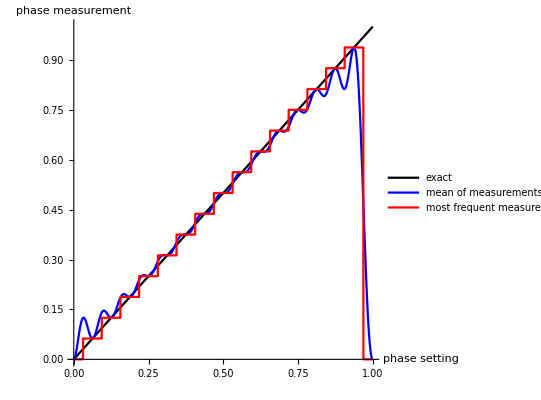

```mathematica
mean[ϕ_?NumericQ]:=prob[ϕ].(Range[0,2^t-1]/2^t);
mostprobable[ϕ_?NumericQ]:=(Ordering[prob[ϕ],-1]⟦1⟧-1)/2^t;
Plot[{ϕ,mean[ϕ],mostprobable[ϕ]},{ϕ,0,1},AxesLabel->{"phase setting","phase measurement"},PlotRange->{{0,1},{0,1}},PlotRangePadding->None,PlotStyle->{Black,{Thick,Blue},{Thick,Red}},AspectRatio->{1},PlotLegends->{"exact","mean of measurements","most frequent measurement"},GridLines->{Range[1,2^t-1]/2^t,Range[1,2^t-1]/2^t}]
```